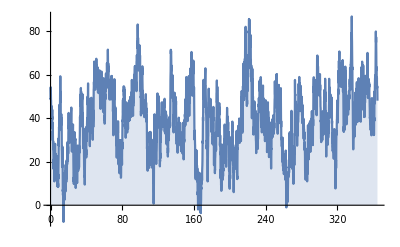

```mathematica
Clear["Global`*"]
(* Generating wealth by power plant operation subject to stochastic processes *)
(* electricty prices move according to an Ornstein-Uhlenbeck Process *)
data=RandomFunction[OrnsteinUhlenbeckProcess[40,12,.3],{0,365,.1}];
ListLinePlot[data,Filling->Axis]
```

```mathematica
Nz=Length[data["Values"]];
G01[x_,ener_]:=Module[{nn=0,j=0,sum=0,prices},
prices=x["Values"];
nn=Length[prices];
For[j=1,j<nn,j++,sum=sum+ener*prices[[j]]];
sum
];
G01[data,1]
```

143563.

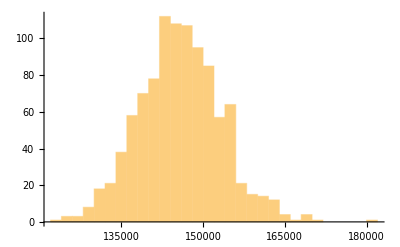

```mathematica
Wealth={};
Nz=1000;
For[j=1,j<Nz,j++,AppendTo[Wealth,G01[RandomFunction[OrnsteinUhlenbeckProcess[40,12,.3],{0,365,.1}],1]]];
Histogram[Wealth]
```